# TP2 : Caméra 2D

## Partie 1: Définir un monde 3D

### 1.1 Le monde en 3D, visualisation d’un dodécahèdre

```mathematica
clear[place3D];
place3D[{posx_,posy_,posz_},angleX_,angleY_,angleZ_,{scalex_,scaley_,scalez_}]:=TranslationTransform[{posx,posy,posz}].RotationTransform[angleX,{1,0,0}].RotationTransform[angleY,{0,1,0}].RotationTransform[angleZ,{0,0,1}].ScalingTransform[{scalex,scaley,scalez}];

place3D[{posx_,posy_,posz_},angleX_,angleY_,angleZ_,scale_]:=place3D[{posx,posy,posz},angleX,angleY,angleZ,{scale,scale,scale}];

place3D[{posx_,posy_,posz_},angleX_,angleY_,angleZ_]:=place3D[{posx,posy,posz},angleX,angleY,angleZ,{1,1,1}];

place3D[{posx_,posy_,posz_}]:=place3D[{posx,posy,posz},0,0,0,{1,1,1}];
```

```mathematica
see3D[e_]:={If[KeyExistsQ[e,"couleur"],e[["couleur"]],Black],If[KeyExistsQ[e,"opacite"],Opacity[e[["opacite"]]],Opacity[1]],Polygon[e[["lignes"]]]};

seeMonde3D[monde_]:=Graphics3D[{see3D/@monde},Boxed->True,Axes->True];

createPolyhedron[polyhedronName_]:=Module[{vertices,faces},vertices=N[PolyhedronData[polyhedronName,"VertexCoordinates"]];
faces=PolyhedronData[polyhedronName,"FaceIndices"];
vertices[[#]]&/@faces];

dodecahedron = createPolyhedron["Dodecahedron"];

monde={
<|"couleur"->Blue,"lignes"->place3D[{0,0,-4}]/@ dodecahedron|>

};

seeMonde3D[monde]
```

-Graphics3D-

### 1.2 Création d’une caméra et prise d’une photo

```mathematica
seeCam3D[w2i_TransformationFunction,width_,height_,depth_]:=Block[{i2w,coinsCam,coinsW,apexCam,apexW},(
i2w=InverseFunction[w2i];
apexCam={0,0,0};
coinsCam={{-width/2,-height/2,-depth},{width/2,-height/2,-depth},{width/2,height/2,-depth},{-width/2,height/2,-depth}};
apexW=i2w[apexCam];
coinsW=i2w/@coinsCam;
Graphics3D[{Blue,PointSize[0.05],Point[apexW],Opacity[0.2],Polygon[coinsW],Line[{apexW,#}]&/@coinsW},Boxed->False,Axes->True])];

xCam=0;
yCam=1;
zCam=3;
cameraAngleX=0;  
cameraAngleY=0;  
cameraAngleZ=0;

f=10;
alpha = 0.2;
cx = 0;
cy = 0;
interne=AffineTransform[{{f,0,cx},{0,alpha f,cy},{0,0,1}}];

cameraToWorld= place3D[{xCam, yCam, zCam}, cameraAngleX, cameraAngleY, cameraAngleZ];
worldToImage=interne.InverseFunction[cameraToWorld];

projectToImage[points3D_List]:=Module[{imagePoints},
imagePoints=worldToImage/@points3D;
{#[[1]]/#[[3]],#[[2]]/#[[3]]}&/@imagePoints];

Show[
seeMonde3D[monde],
seeCam3D[worldToImage, 10,10,2]
]
```

-Graphics3D-

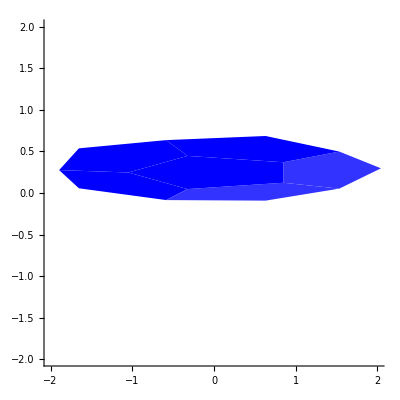

```mathematica
viewDirection={0,0,1};
lightDirection=Normalize[{1,-1,-1}];
calculateBrightness[normal_]:=Max[0,normal.lightDirection];
computeNormal[face_List]:=Module[{v1,v2,normal},v1=face[[2]]-face[[1]];
v2=face[[3]]-face[[1]];
normal=Normalize[Cross[v1,v2]];
normal];
renderMonde2D[monde_List,projectToImage_]:=Module[{projectedScenes,scene2D,brightness,color,normal},projectedScenes=Table[Table[normal=computeNormal[monde[[i,"lignes",j]]];
If[normal.viewDirection<0,brightness=calculateBrightness[normal];
color=Lighter[monde[[i,"couleur"]],0.2-brightness];
{color,Polygon[projectToImage[monde[[i,"lignes",j]]]]},Nothing],{j,Length[monde[[i,"lignes"]]]}],{i,Length[monde]}];
scene2D=Flatten[{PointSize[0.02],projectedScenes}];
Graphics[scene2D,PlotRange->{{-2,2},{-2,2}},Axes->True]];

renderMonde2D[monde, projectToImage]
```

## Partie 2: Calibration d’une caméra avec un objet 3D

```mathematica
points3D = monde[[1,"lignes"]];
points2D ={projectToImage[#] &/@ monde[[1,"lignes"]]}[[1]];
```

```mathematica
(*Trouver les coefficients en 3D*)
m3x4={{m1,m2,m3,m4},{m5,m6,m7,m8},{m9,m10,m11,m12}};
eq=Cross[m3x4.{x,y,z,1},{xi,yi,1}];
Coefficient[#,{m1,m2,m3,m4,m5,m6,m7,m8,m9,m10,m11,m12}]&/@eq
```

{{0,0,0,0,x,y,z,1,-x yi,-y yi,-yi z,-yi},{-x,-y,-z,-1,0,0,0,0,x xi,xi y,xi z,xi},{x yi,y yi,yi z,yi,-x xi,-xi y,-xi z,-xi,0,0,0,0}}

```mathematica
diagonalePositive[{r_,q_}]:=Block[{s},(
s=DiagonalMatrix[Sign[Diagonal[r]]];
{r.s,s.q}
)];

RQDecompV1[a_]:=Block[{r1,q1},(
{q1,r1}=QRDecomposition[Transpose[Reverse[a]]];
q1=Transpose[q1]; (* a cause de mathematica *)
r1=Reverse[Transpose[Reverse[r1]]];
q1=Reverse[Transpose[q1]];
diagonalePositive[{r1,q1}]
)];

ligne3D[{x_,y_,z_},{xi_,yi_}]:={{0,0,0,0,x,y,z,1,-x yi,-y yi,-yi z,-yi},{-x,-y,-z,-1,0,0,0,0,x xi,xi y,xi z,xi}};


ma  = Table[ligne3D[points3D[[i,1]],points2D[[i,1]]],{i,8}];
ma = Flatten[ma,{{1,2},{3}}];

{u,w,v} = SingularValueDecomposition[ma];

P=Partition[v[[All,-1]],4];
P = P /P[[3,3]];

H  = P[[;;3,;;3]];
{K,R} = RQDecompV1[H];
K/K[[3,3]]//MatrixForm//Chop
T =Inverse[H].P[[All,-1]] //MatrixForm //Chop
R // MatrixForm//Chop
```

(10. | 0 | 0
0 | 2. | 0
0 | 0 | 1.)

(0
-1.
-3.)

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

## Partie 3: Calibration planaire

```mathematica
boardPos = {-5,-5,0.0};
boardSize=8;
squareSize=1;
thickness=0.1; 

board =Table[<|{If[EvenQ[i+j],"couleur"->Black,"couleur"->White],"lignes"->place3D[boardPos + {i,j,0},0,0,0,{1,1,0}]/@cube}|>,{i,0,boardSize-1},{j,0,boardSize-1}];
board = Flatten[board,{{1,2}}];


Show[
seeMonde3D[board],
seeCam3D[worldToImage, 40,40,2]
]
```

-Graphics3D-

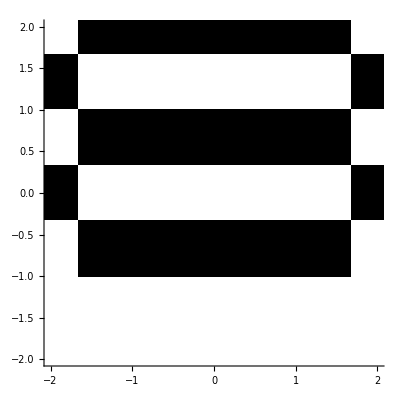

```mathematica
renderMonde2D[board, projectToImage]
```

#### Prise de multiples photos...

```mathematica
CreateProjectionFunction[xCam_,yCam_,zCam_,cameraAngleX_,cameraAngleY_,cameraAngleZ_,interne_]:=Module[{cameraToWorld,worldToImage,projectToImage},
cameraToWorld=place3D[{xCam,yCam,zCam},cameraAngleX,cameraAngleY,cameraAngleZ];
worldToImage=interne.InverseFunction[cameraToWorld];
projectToImage[points3D_List]:=Module[{imagePoints},imagePoints=worldToImage/@points3D;
{#[[1]]/#[[3]],#[[2]]/#[[3]]}&/@imagePoints];
projectToImage];

points3DGrid = Table[board[[i,"lignes",5]],{i,Length[board]}];
points3DGridFlatten = Flatten[points3DGrid, {{1,2},{3}}];

points2DGrid = projectToImage/@ points3DGrid;
points2DGridFlatten = Flatten[points2DGrid,{{1,2},{3}}];
renderMonde2D[board, projectToImage];

projectToImage0 = CreateProjectionFunction[1,0,10,Pi/8,0,0,interne];
points2DGrid0 = projectToImage0/@points3DGrid;
points2DGridFlatten0 = Flatten[points2DGrid0,{{1,2},{3}}];
renderMonde2D[board, projectToImage0];

projectToImage1 = CreateProjectionFunction[1,0.2,10,0.2,Pi/4,0,interne];
points2DGrid1 = projectToImage1/@points3DGrid;
points2DGridFlatten1 = Flatten[points2DGrid1,{{1,2},{3}}];
renderMonde2D[board, projectToImage1];

projectToImage2 = CreateProjectionFunction[1,0,15,0.2,-0.2,Pi/2,interne];
points2DGrid2 = projectToImage2/@points3DGrid;
points2DGridFlatten2 = Flatten[points2DGrid2,{{1,2},{3}}];
renderMonde2D[board, projectToImage2];

projectToImage3 = CreateProjectionFunction[1,0,10,0.1,0.05,0,interne];
points2DGrid3 = projectToImage3/@points3DGrid;
points2DGridFlatten3 = Flatten[points2DGrid3,{{1,2},{3}}];
renderMonde2D[board, projectToImage3];

views = {points2DGridFlatten,points2DGridFlatten0,points2DGridFlatten1,points2DGridFlatten2,points2DGridFlatten3};
```

### Calibrage...

```mathematica
(* Fonction pour trouver les coefficients *)
```

```mathematica
h = {{g1,g2,g3},{g4,g5,g6},{g7,g8,g9}};
W={{w1,0,w4},{0,w2,w5},{w4,w5,w3}};

lignes[ {{g1_,g2_,g3_},{g4_,g5_,g6_},{g7_,g8_,g9_}}]= {
 Coefficient[h[[All,1]].W.h[[All,2]],{w1,w2,w3,w4,w5}],
Coefficient[h[[All,1]].W.h[[All,1]] -h[[All,2]].W.h[[All,2]],{w1,w2,w3,w4,w5}]
};
```

```mathematica
(*Trouver la matrice W*)
homographies=Table[TransformationMatrix[FindGeometricTransform[views[[i]], points3DGridFlatten[[All,1;;2]]][[2]]],{i,Length[views]}];
ma = Flatten[Table[lignes[homographies[[i]]], {i, Length[homographies]}],{{1,2},{3}}];
{u,w,v} = SingularValueDecomposition[ma];
mw = v[[All,-1]];
wFinal ={{mw[[1]],0,mw[[4]]},{0,mw[[2]],mw[[5]]},{mw[[4]],mw[[5]],mw[[3]]}};
wFinal = wFinal/wFinal[[2,2]]
```

{{0.25,0.,-5.},{0.,1.,1.46737×10^-14},{-5.,1.46737×10^-14,125.}}

```mathematica
(*Trouver la matrice interne*)
a = Sqrt[wFinal[[1,1]]];
v = -wFinal[[2,3]];
u = -wFinal[[1,3]]/Power[a,2];
f = wFinal[[3,3]] - Power[v,2] - Power[a,2]Power[u,2];
f = f /Power[a,2];
f = Sqrt[f];
matriceInterne = {{f,0,u},{0,a f,v},{0,0,1}}//MatrixForm //Chop
```

(10. | 0 | 20.
0 | 5. | 0
0 | 0 | 1)